# 2D First-Passage time

## Drift towards the equilibrium at (x~, y~) = (0, 0) with an absorbing boundary at x~=x~*.

## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP=λt*D[yt*P[xt, yt], xt]+κt*D[yt*P[xt, yt], yt]-κt*D[xt*P[xt, yt],yt]+(1/2)D[P[xt, yt],{xt,2}]+(κt^2/2)*D[P[xt, yt],{yt,2}];
```

## Get the steady-state variances

```mathematica
A= {{ 0,λt},{-κt, κt}}
B = {{1,0},{0,κt}}
s=Array[Y,{2,2}]
ss =( s/. Expand[FullSimplify[Solve[A.s+s.Transpose[A]==B.Transpose[B], Flatten[s]]]])[[1]]
```

{{0,λt},{-κt,κt}}

{{1,0},{0,κt}}

{{Y[1,1],Y[1,2]},{Y[2,1],Y[2,2]}}

{{1/(2 κt)+1/(2 λt)+λt/2,1/(2 λt)},{1/(2 λt),κt/2+1/(2 λt)}}

## Choose the parameter values

```mathematica
λts = {0.1, 0.5, 1.0, 1.5, 2};
κts = {10, 11, 12, 13,14};
κScale = Flatten[Table[κts^2/2, 5]] (*For scaling the flux to a probability distribtion*)
params = Flatten[Table[{λt->l, κt->k}, {l, λts}, {k, κts}], 1]
legend =  Flatten[Table["λt="<>ToString[l]<>"; "<> "κt="<>ToString[k], {l, λts},{k, κts}], 1];
products = Table[i*j, {i, λts}, {j, κts}]
```

{50,121/2,72,169/2,98,50,121/2,72,169/2,98,50,121/2,72,169/2,98,50,121/2,72,169/2,98,50,121/2,72,169/2,98}

{{λt→0.1,κt→10},{λt→0.1,κt→11},{λt→0.1,κt→12},{λt→0.1,κt→13},{λt→0.1,κt→14},{λt→0.5,κt→10},{λt→0.5,κt→11},{λt→0.5,κt→12},{λt→0.5,κt→13},{λt→0.5,κt→14},{λt→1.,κt→10},{λt→1.,κt→11},{λt→1.,κt→12},{λt→1.,κt→13},{λt→1.,κt→14},{λt→1.5,κt→10},{λt→1.5,κt→11},{λt→1.5,κt→12},{λt→1.5,κt→13},{λt→1.5,κt→14},{λt→2,κt→10},{λt→2,κt→11},{λt→2,κt→12},{λt→2,κt→13},{λt→2,κt→14}}

{{1.,1.1,1.2,1.3,1.4},{5.,5.5,6.,6.5,7.},{10.,11.,12.,13.,14.},{15.,16.5,18.,19.5,21.},{20,22,24,26,28}}

## Get the trajectory of the mean

```mathematica
eig=FullSimplify[Eigenvectors[A]]
```

{{1/2 (1+(√(κt-4 λt))/(√κt)),1},{1/2-(√(κt-4 λt))/(2 √κt),1}}

```mathematica
cstar = Flatten[Table[(1/2 (1+(√(κt-4 λt))/(√κt)))^-1/.p, {p, params}]]
```

{1.01021,1.00926,1.00848,1.00781,1.00725,1.05573,1.05013,1.04555,1.04174,1.03852,1.12702,1.11252,1.10102,1.09167,1.08392,1.22515,1.1946,1.17157,1.15354,1.139,2/(1+1/(√5)),2/(1+√(3/11)),2/(1+1/(√3)),2/(1+√(5/13)),2/(1+√(3/7))}

## Set up the mesh, boundary conditions, and initial condition

#### Steady-state distribution widths in x~, y~

```mathematica
xtwidths =N[ Table[ss[[1,1]]/.p, {p, params}]]
ytwidths = N[Table[ss[[2,2]]/.p, {p, params}]]
xywidths =N[ Table[ss[[1,2]]/.p, {p, params}]]
```

{5.1,5.09545,5.09167,5.08846,5.08571,1.3,1.29545,1.29167,1.28846,1.28571,1.05,1.04545,1.04167,1.03846,1.03571,1.13333,1.12879,1.125,1.12179,1.11905,1.3,1.29545,1.29167,1.28846,1.28571}

{10.,10.5,11.,11.5,12.,6.,6.5,7.,7.5,8.,5.5,6.,6.5,7.,7.5,5.33333,5.83333,6.33333,6.83333,7.33333,5.25,5.75,6.25,6.75,7.25}

{5.,5.,5.,5.,5.,1.,1.,1.,1.,1.,0.5,0.5,0.5,0.5,0.5,0.333333,0.333333,0.333333,0.333333,0.333333,0.25,0.25,0.25,0.25,0.25}

Choose the widest distribution

```mathematica
xtvarChoice=1;
ytvarChoice=5;
xyvarChoice = 1;
```

Initial stds in x~, y~

```mathematica
xtStds = Table[Sqrt[xtwidths[[xtvarChoice]]],Length[params]]
ytStds = Table[Sqrt[ytwidths[[ytvarChoice]]],Length[params]]
```

{2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832,2.25832}

{3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641,3.4641}

#### Boundary condition at x~* -> y~* = c* x~*. Choose the boundaries to be far enough away from the initial condition and the final distribution

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
xt0 = 20;
xtls=-5*xtStds
xtrs = xt0+5*xtStds
ytls=cstar
ytrs = cstar*xt0+5*ytStds
```

{-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916,-11.2916}

{31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916,31.2916}

{1.01021,1.00926,1.00848,1.00781,1.00725,1.05573,1.05013,1.04555,1.04174,1.03852,1.12702,1.11252,1.10102,1.09167,1.08392,1.22515,1.1946,1.17157,1.15354,1.139,2/(1+1/(√5)),2/(1+√(3/11)),2/(1+1/(√3)),2/(1+√(5/13)),2/(1+√(3/7))}

{37.5246,37.5057,37.49,37.4768,37.4654,38.4351,38.323,38.2315,38.1553,38.0909,39.8608,39.5709,39.3409,39.154,38.9989,41.8235,41.2125,40.752,40.3912,40.1005,44.9598,43.5977,42.6795,42.0092,41.4948}

```mathematica
icPos =Table[{xt0, c*xt0}, {c, cstar}];
icVar =1.05*{{xtwidths[[xtvarChoice]], xywidths[[xyvarChoice]]},{xywidths[[xyvarChoice]], ytwidths[[ytvarChoice]]}}
ic0 = N[Table[PDF[MultinormalDistribution[pos,icVar], {xt, yt}], {pos, icPos}]];
bcFunc[xtl_, xtr_, ytl_, ytr_] :={
	  P[xtl, yt]==0,
           P[xtr, yt]==0,
           P[xt, ytr]==0,
           P[xt, ytl]==0
};
ΩFunc[xtl_, xtr_, ytl_, ytr_] :=ImplicitRegion[True,{{xt,xtl,xtr},{yt,ytl,ytr}}];
bcs = MapThread[bcFunc, {xtls, xtrs, ytls, ytrs}];
cellDistances = Table[Min[ytStds]/100, 25]
Ω=MapThread[ΩFunc,{xtls, xtrs, ytls, ytrs}];
```

{{5.355,5.25},{5.25,12.6}}

{0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641,0.034641}

```mathematica
ytCheckFunc[ytl_, c_]:=c≤ ytl
```

```mathematica
MapThread[ytCheckFunc, {cstar*xt0-5*ytStds, cstar}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

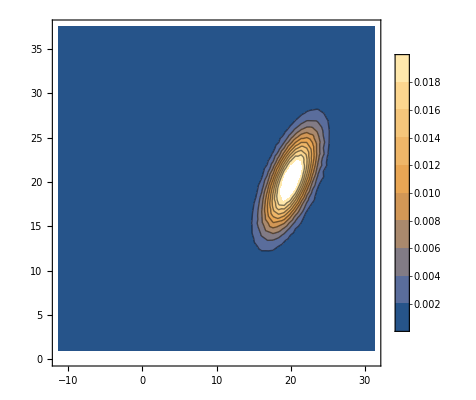

```mathematica
toPlot=1;
ContourPlot[ic0[[toPlot]], {xt, xtls[[toPlot]], xtrs[[toPlot]]}, {yt, ytls[[toPlot]], ytrs[[toPlot]]}, PlotRange->{0, 0.02}, PlotLegends->Automatic]
```

## Calculate the time-integrated probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, reg_, cell_] :=Module[{N},
N = NDSolve[Join[{(FP/. param)==-ic}, bc],
                                   P,{xt, yt}∈reg, 
Method->{"FiniteElement", "MeshOptions"->{"MaxCellMeasure"->cell}}];
Return[(P/.N[[1]])];
]
```

```mathematica
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, Ω, cellDistances}];
```

```mathematica
solsIc0[[1]]["ElementMesh"]["Wireframe"]
```

-Graphics-

```mathematica
fluxXIc0 = Table[Derivative[0,1][sol],{sol, solsIc0}];
```

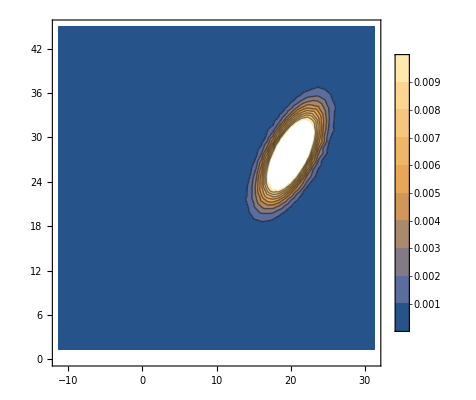

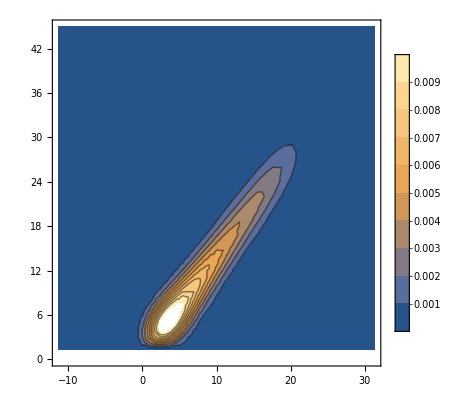

```mathematica
toPlot=21;
ContourPlot[ic0[[toPlot]], {xt, xtls[[toPlot]], xtrs[[toPlot]]}, {yt, ytls[[toPlot]], ytrs[[toPlot]]}, PlotRange->{0, 0.01}, PlotLegends->Automatic]
ContourPlot[solsIc0[[toPlot]][xt, yt], {xt, xtls[[toPlot]], xtrs[[toPlot]]}, {yt, ytls[[toPlot]], ytrs[[toPlot]]}, PlotLegends->Automatic, PlotRange->{0,0.01}]
```

```mathematica
XIc0 =(MapThread[#1[xt,#2]&,{fluxXIc0,ytls}])*κScale;
```

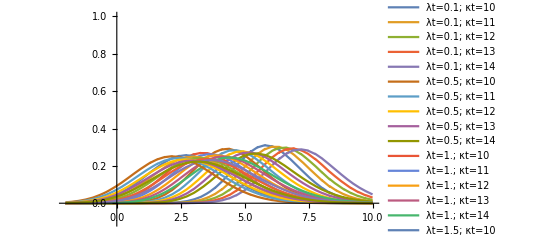

```mathematica
Plot[XIc0, {xt, -2, 10}, PlotRange->{-0.1, 1}, PlotLegends->legend]
```

```mathematica
IntegFunc[f_, l_, r_] := NIntegrate[f, {xt, l, r}, WorkingPrecision->10]
```

```mathematica
normsIc0 = MapThread[IntegFunc, {XIc0, xtls/2, xtrs/2}]
corrected = MapThread[#1/#2&, {XIc0, normsIc0}];
meansIc0= MapThread[IntegFunc, {XIc0*xt, xtls, xtrs}]
secondIc0 = MapThread[IntegFunc, {XIc0*xt*xt, xtls, xtrs}]
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0^2;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {5.24868933}. NIntegrate obtained 0.9979412023 and 0.0001937474225 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.9979412023,0.9978578244,0.9979810219,0.9982357953,0.9983419083,0.9999102428,0.9995390915,1.000009827,0.9994839593,0.9993192932,1.000620694,1.000590353,1.000087357,1.000288767,1.000115313,1.000218518,1.000889999,1.000643255,1.000572015,1.000441762,1.000709604,1.000799182,1.0004806,1.00048351,1.000635714}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {7.253738028}. NIntegrate obtained 5.939337259 and 0.001584147938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {7.253738028}. NIntegrate obtained 6.307453987 and 0.001402736235 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {8.334951572}. NIntegrate obtained 6.662185959 and 0.001924513262 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{5.939337259,6.307453987,6.662185959,7.002034132,7.332617815,4.477247825,4.787984198,5.087965524,5.377268059,5.657151171,3.550748151,3.842348534,4.122518653,4.393626527,4.654432364,2.877565306,3.165830753,3.439548616,3.70176432,3.955382841,2.285969118,2.587107061,2.867036091,3.130654557,3.38380873}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {7.253738028}. NIntegrate obtained 37.0574868 and 0.01050966363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {7.253738028}. NIntegrate obtained 41.64716563 and 0.01026538886 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {8.334951572}. NIntegrate obtained 46.31827279 and 0.01350394451 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{37.0574868,41.64716563,46.31827279,51.05134606,55.86047744,22.0031798,24.99276151,28.06234954,31.19510547,34.38520085,14.85921229,17.14833887,19.51165255,21.94403682,24.42776489,10.73393274,12.62655822,14.58403613,16.60976292,18.69512613,7.769012312,9.435115864,11.14303428,12.89734416,14.70909762}

{1.7817597,1.8631898,1.933551,2.0228641,2.0931934,1.9574317,2.0679688,2.1749564,2.2800937,2.3818415,2.2513999,2.3846966,2.5164925,2.6400828,2.7640243,2.4535506,2.6040739,2.7535414,2.9067038,3.0500727,2.5433575,2.74199292,2.92313833,3.0963462,3.2589361}

```mathematica
grid = Flatten[Table[{l, s}, {l, λts}, {s, κts}], 1];
params
```

{{λt→0.1,κt→10},{λt→0.1,κt→11},{λt→0.1,κt→12},{λt→0.1,κt→13},{λt→0.1,κt→14},{λt→0.5,κt→10},{λt→0.5,κt→11},{λt→0.5,κt→12},{λt→0.5,κt→13},{λt→0.5,κt→14},{λt→1.,κt→10},{λt→1.,κt→11},{λt→1.,κt→12},{λt→1.,κt→13},{λt→1.,κt→14},{λt→1.5,κt→10},{λt→1.5,κt→11},{λt→1.5,κt→12},{λt→1.5,κt→13},{λt→1.5,κt→14},{λt→2,κt→10},{λt→2,κt→11},{λt→2,κt→12},{λt→2,κt→13},{λt→2,κt→14}}

```mathematica
normArrayIc0 = ArrayReshape[normsIc0, {5,5}];
varArrayIc0 = ArrayReshape[varsIc0, {5,5}];
meanArrayIc0 = ArrayReshape[meansIc0, {5,5}];
diffArrayIc0 = ArrayReshape[diffIc0, {5,5}];
```

```mathematica
cf[x_]:=Blend[{{0, Red},{ 1,White},{5,Blue}}, x]
xticks = Transpose[{{1, 2, 3, 4, 5}, λts}];
yticks = Transpose[{{1, 2, 3, 4, 5}, κts}];
```

```mathematica
varArrayIc0;
meanArrayIc0
```

{{5.939337259,6.307453987,6.662185959,7.002034132,7.332617815},{4.477247825,4.787984198,5.087965524,5.377268059,5.657151171},{3.550748151,3.842348534,4.122518653,4.393626527,4.654432364},{2.877565306,3.165830753,3.439548616,3.70176432,3.955382841},{2.285969118,2.587107061,2.867036091,3.130654557,3.38380873}}

```mathematica
ArrayPlot[varArrayIc0, ColorFunction->(Blend[{{ -0.2,White},{2,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var("OverTilde[xt]   .")"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]

ArrayPlot[ArrayReshape[Table[Blend[{{0, Red},{ 1,White},{5,Blue}}, i],{i,Flatten[meanArrayIc0]}], {5,5}], PlotLegends->{Placed[BarLegend[{cf[#]&,{0, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]

ArrayPlot[diffArrayIc0, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"varScaledToMean2(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]
```

-Graphics-

-Graphics-

-Graphics-

#### Check that all s.s. variances have been reached before mean passage

```mathematica
S[A_, B_] := FullSimplify[Integrate[MatrixExp[-A*(t-tp)].B.Transpose[B].MatrixExp[-Transpose[A]*(t-tp)], {tp, 0, t}]];
```

```mathematica
As = {{ 0,λ},{-κ, 1}}
Bs = {{1,0},{0,κ }}
s0[λ_, κ_, t_] = FullSimplify[MatrixExp[-{{ 0,λ},{-κ, 1}}*t].icVar.MatrixExp[-Transpose[{{ 0,λ},{-κ, 1}}]*t]];
```

{{0,λ},{-κ,1}}

{{1,0},{0,κ}}

{{1/(-0.25+1. κ λ)(ⅇ^-t λ (-2.5+12.755 κ+1.17563 λ)+ⅇ^(-t (1+√(1-4 κ λ))) (-3.18875+3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ-1.25 √(1-4 κ λ)))+ⅇ^(t (-1+√(1-4 κ λ))) (-3.18875-3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ+1.25 √(1-4 κ λ)))),1/(-0.25+1. κ λ)(-3.18875 Cosh[t]+3.18875 Sinh[t]) (0.392003-2. κ-0.184339 λ+(κ (2.-1.56801 λ)+0.184339 λ) Cosh[t √(1-4 κ λ)]+2. (1. κ-0.0921697 λ) √(1-4 κ λ) Sinh[t √(1-4 κ λ)])},{1/(-0.25+1. κ λ)(-3.18875 Cosh[t]+3.18875 Sinh[t]) (0.392003-2. κ-0.184339 λ+(κ (2.-1.56801 λ)+0.184339 λ) Cosh[t √(1-4 κ λ)]+2. (1. κ-0.0921697 λ) √(1-4 κ λ) Sinh[t √(1-4 κ λ)]),1/(-0.25+1. κ λ)(ⅇ^-t κ (-2.5+12.755 κ+1.17563 λ)+ⅇ^(t (-1+√(1-4 κ λ))) (-0.293906+0.293906 √(1-4 κ λ)+κ (1.25-6.3775 κ+0.587813 λ-1.25 √(1-4 κ λ)))+ⅇ^(-t (1+√(1-4 κ λ))) (-0.293906-0.293906 √(1-4 κ λ)+κ (1.25-6.3775 κ+0.587813 λ+1.25 √(1-4 κ λ))))}}

```mathematica
S0 =%532[[1,1]];
```

1/(-0.25+1. κ λ)(ⅇ^-t λ (-2.5+12.755 κ+1.17563 λ)+ⅇ^(-t (1+√(1-4 κ λ))) (-3.18875+3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ-1.25 √(1-4 κ λ)))+ⅇ^(t (-1+√(1-4 κ λ))) (-3.18875-3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ+1.25 √(1-4 κ λ))))

```mathematica
curve =S[As, Bs];
```

{{(((1-ⅇ^(-t (1+√(1-4 κ λ)))) (-1+√(1-4 κ λ)-2 κ λ (-1+κ λ)))/(1+√(1-4 κ λ))-((-1+ⅇ^(t (-1+√(1-4 κ λ)))) (1+√(1-4 κ λ)+2 κ λ (-1+κ λ)))/(-1+√(1-4 κ λ))+4 κ λ (1+κ λ) (1-Cosh[t]+Sinh[t]))/(-2+8 κ λ),(ⅇ^(-t (2+√(1-4 κ λ))) (-4 ⅇ^(t (1+√(1-4 κ λ))) κ λ (1+κ λ)+ⅇ^(t (2+√(1-4 κ λ))) (-2+8 κ λ)+ⅇ^t (1-√(1-4 κ λ)+2 κ λ (-1+κ λ))+ⅇ^(t+2 t √(1-4 κ λ)) (1+√(1-4 κ λ)+2 κ λ (-1+κ λ))))/(4 λ (-1+4 κ λ))},{(ⅇ^(-t (2+√(1-4 κ λ))) (-4 ⅇ^(t (1+√(1-4 κ λ))) κ λ (1+κ λ)+ⅇ^(t (2+√(1-4 κ λ))) (-2+8 κ λ)+ⅇ^t (1-√(1-4 κ λ)+2 κ λ (-1+κ λ))+ⅇ^(t+2 t √(1-4 κ λ)) (1+√(1-4 κ λ)+2 κ λ (-1+κ λ))))/(4 λ (-1+4 κ λ)),(κ^2 (-((1-ⅇ^(-t (1+√(1-4 κ λ)))) (3-2 κ λ+√(1-4 κ λ)))/(1+√(1-4 κ λ))+((-1+ⅇ^(t (-1+√(1-4 κ λ)))) (-3+2 κ λ+√(1-4 κ λ)))/(-1+√(1-4 κ λ))+4 (1+κ λ) (1-Cosh[t]+Sinh[t])))/(-2+8 κ λ)}}

```mathematica
toPlotCurve[λ_, κ_, t_]=1.05S0+curve[[1,1]];
```

1/(-0.25+1. κ λ)1.05 (ⅇ^-t λ (-2.5+12.755 κ+1.17563 λ)+ⅇ^(-t (1+√(1-4 κ λ))) (-3.18875+3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ-1.25 √(1-4 κ λ)))+ⅇ^(t (-1+√(1-4 κ λ))) (-3.18875-3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ+1.25 √(1-4 κ λ))))+(((1-ⅇ^(-t (1+√(1-4 κ λ)))) (-1+√(1-4 κ λ)-2 κ λ (-1+κ λ)))/(1+√(1-4 κ λ))-((-1+ⅇ^(t (-1+√(1-4 κ λ)))) (1+√(1-4 κ λ)+2 κ λ (-1+κ λ)))/(-1+√(1-4 κ λ))+4 κ λ (1+κ λ) (1-Cosh[t]+Sinh[t]))/(-2+8 κ λ)

```mathematica
Manipulate[Plot[{toPlotCurve[λ, κ, t], 1/2+1/(2 κ λ)+(κ λ)/2}, {t, 0, 35}, PlotRange->{0, 35}, GridLines->{{{tfPlot [λ, κ, 8],Red}},None}], {λ, 0.01, 0.5}, {κ, 0.2, 0.45}]
```

```mathematica
tfPlot [λ_, κ_, x0_] := (1/λ)*Log[x0/(2*κ/(1+Sqrt[1-4*λ*κ]))]
```